#### n=20

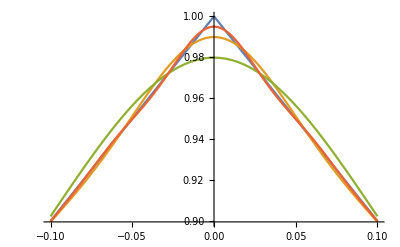

```mathematica
Plot[{Piecewise[{{x+1, -1≤x<0}, {1-x, 0≤x<1}}], 0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 20}], 0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 10}], 0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 40}]}, {x,-.1, .1}]
```

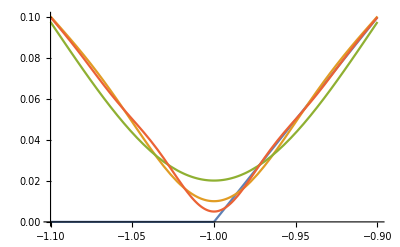

```mathematica
Plot[{Piecewise[{{x+1, -1≤x<0}, {1-x, 0≤x<1}}], 0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 20}], 0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 10}], 0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 40}]}, {x,-1.1, -0.9}]
```

```mathematica
f[x_]:=Piecewise[{{x+1, -1≤x<0}, {1-x, 0≤x<1}}]
```

```mathematica
g[x_]:=0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 20}]
```

```mathematica
h[x_]:=0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 10}]
```

```mathematica
i[x_]:=0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 40}]
```

```mathematica
{f[1]-g[1], f[1]-h[1], f[1]-i[1]}
```

{-0.0101237,-0.0201976,-0.005065}

```mathematica
{f[0]-g[0], f[0]-h[0], f[0]-i[0]}
```

{0.0101237,0.0201976,0.005065}

```mathematica
{f[-1]-g[-1], f[-1]-h[-1], f[-1]-i[-1]}
```

{-0.0101237,-0.0201976,-0.005065}

#### part c

```mathematica
k[x_]:=0.5+Sum[(2+2*((-1)^(m+1)))*Cos[m*Pi*x]/(m*Pi)^2, {m, 1, 21}]
```

```mathematica
f[1]-k[1]
```

-0.00920469